```mathematica
Quit
```

```mathematica
SetDirectory[NotebookDirectory[]];
(* Vanilla wCDM *)
dLwCDM[a_,om_,w_]:=2/(a √om)(Hypergeometric2F1[1/2,-1/(6w),1-1/(6w),1-1/om]-√a Hypergeometric2F1[1/2,-1/(6w),1-1/(6w),(1-1/om)a^(-3w)]);
HwCDM[a_,w_,om_]:=√(om a^-3+(1-om)a^(-3(1+w)));
(* Growth for wCDM models *)
δwCDM[a_,w_,Ω_]:=a Hypergeometric2F1[1/(-3w),1/2-1/(2 w),1-5/(6 w),a^(-3 w) (1-1/Ω)]
fwCDM[a_,w_,Ω_]:=aa D[Log[δwCDM[aa,w,Ω]],aa]/.aa->a
fσ8wCDM[a_,w_,Ω_,σ8_]:=fwCDM[a,w,Ω]σ8  δwCDM[a,w,Ω]/δwCDM[1,w,Ω]
ΣwCDM[a_,w_,Ω_]:=2
ηwCDM[a_,w_,Ω_]:=1
EgwCDM[a_,w_,Ω_]:=(Ω ΣwCDM[a,w,Ω])/(2fwCDM[a,w,Ω])
P2wCDM[a_,w_,Ω_]:=2 EgwCDM[a,w,Ω]
P3wCDM[a_,w_,Ω_,σ8_]:=a D[Log[fσ8wCDM[aa,w,Ω,σ8]],aa]/.aa->a
```

```mathematica
ϵ0={-1,0,1};
```

```mathematica
(* CC data *)
EGA[a_]:=√(1+z (-0.8999883844902956+0.2620381909322407 (1+0.15327819800211584 z)^3-0.381979946511561 (1+1.6189955164319452 z))^2)/.z->1/a-1;
H0GA=67.17004414248437;
fminerrH={20.889676091967573,{a1->0.18193760065911452,a2->0.20201812774843367}};
dH[z_,a1_,a2_,a3_,a4_]:=a1+a2 z+a3 z^2+a4 z^4
δEGA[a_]:=dH[1/a-1,a1,a2,0,0]/.fminerrH[[2]];
```

```mathematica
σH0->(H0GA(EGA[a]+ϵ0 δEGA[a])/.a->1//Differences//Mean)
```

σH0→12.2208

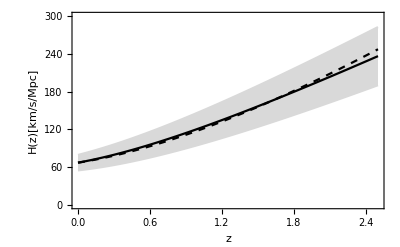

```mathematica
Plot[H0GA{HwCDM[a,-1,0.3],EGA[a]+ϵ0 δEGA[a]}/.a->1/(1+z)//Evaluate,{z,0,2.5},Frame->True,PlotRange->{0,300},PlotStyle->{{Dashed,Black},LightGray,Black,LightGray},Filling->{2->{{4},LightGray}},FrameStyle->Black,FrameLabel->{"z","H(z)[km/s/Mpc]"}]
```

```mathematica
(* growth data *)
fs8GA0[a_]:=a-a^4 (-0.4115523329512044 a^1.5332714921897406+0.002887890644749495 a^5.680438572566711+1.6801627335784026 (0.07258660144352902^(0.07258660144352902 a) a^(0.07258660144352902 a))^1.7198211539830677)^2
fs8c0=1.10938192906447;
fs8GA[a_]:=fs8c0 fs8GA0[a]
dfs8[a_,a1_,a2_,a3_,a4_]:=a(a1+a2 a+a3 a^2)
fminfs8err={17.547530221462015,{a1->-0.3535053502135364,a2->0.2565032464688286}};
δfs8GA[a_]:=dfs8[a,a1,a2,0,0]/.fminfs8err[[2]]
fGA[a_?NumericQ]:=fs8GA[a]/NIntegrate[fs8GA[x]/x,{x,0,a}]
δfGA[a_?NumericQ]:=fGA[a]/fs8GA[a](δfs8GA[a]-fGA[a]NIntegrate[δfs8GA[aa]/aa,{aa,0,a}])
```

```mathematica
fs8GA[a]/fs8GA0[a]/.a->1
```

1.10938

```mathematica
Subscript[σf, 0]->((fs8GA[a]+ϵ0 δfs8GA[a])/fs8GA0[a]/.a->1//Differences//Mean//Abs)
```

σf_0→0.272285

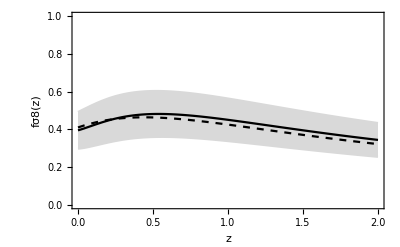

```mathematica
Plot[{fσ8wCDM[1/(1+z),-1,0.3,0.8],fs8GA[1/(1+z)]+ϵ0 δfs8GA[1/(1+z)]}//Evaluate,{z,0,2},Frame->True,PlotRange->{0,1},PlotStyle->{{Dashed,Black},LightGray,Black,LightGray},Filling->{2->{{4},LightGray}},FrameStyle->Black,FrameLabel->{"z","fσ8(z)"}]
```

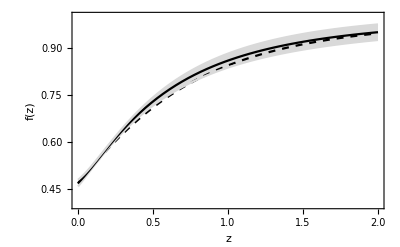

```mathematica
Plot[{fwCDM[1/(1+z),-1,0.255],fGA[1/(1+z)]+ϵ0 δfGA[1/(1+z)]}//Evaluate,{z,0,2},Frame->True,PlotRange->{0.4,1},PlotRange->{0,1},PlotStyle->{{Dashed,Black},LightGray,Black,LightGray},Filling->{2->{{4},LightGray}},FrameStyle->Black,FrameLabel->{"z","f(z)"}]
```

```mathematica
(* P2 calculation *)
(*P2GA[a_]:=(-2.869194969500254 a^3+4.758103253931106 a^9-0.15975098755191963 0.18034521663304748^(0.36069043326609496 a) a^(0.36069043326609496 a))^2
dP2[a_,a1_,a2_,a3_]:=a1+a2 (a-1)+a3 (a-1)^2
fminP2err={8.072703338209434,{a1->0.08190462324525495,a2->0.1268718506423952}}*)
```

```mathematica
(* P2 calculation *)
P2GA[a_]:=0.06336767999292814+a^3 (1.3692920790938419+2.3721591212291947*^-11 a^18)^2
dP2[a_,a1_,a2_,a3_]:=a1+a2 (a-1)+a3 (a-1)^2
fminP2err={9.932640981816341,{a1->0.10304952434304888,a2->0.19499621929471425}};
δP2GA[a_]:=dP2[a,a1,a2,0]/.fminP2err[[2]]
```

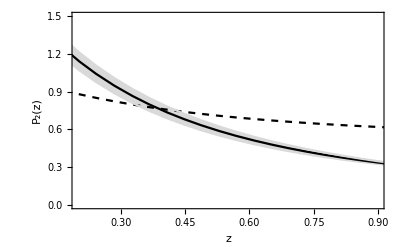

```mathematica
Plot[{P2wCDM[1/(1+z),-1,0.255],P2GA[1/(1+z)]+ϵ0 δP2GA[1/(1+z)]}//Evaluate,{z,0,2},Frame->True,PlotRange->{{0.2,0.9},{0,1.5}},PlotStyle->{{Dashed,Black},LightGray,Black,LightGray},Filling->{2->{{4},LightGray}},FrameStyle->Black,FrameLabel->{"z","P_2(z)"}]
```

```mathematica
(* P3 calculation *)
P3GA[a_]:=a D[Log[fs8GA[A]],A]/.A->a
δP3GA[a_?NumericQ]:=-aa(δfs8GA[aa] D[fs8GA[aa],aa])/fs8GA[aa]^2+aa D[δfs8GA[aa],aa]/fs8GA[aa]/.aa->a
```

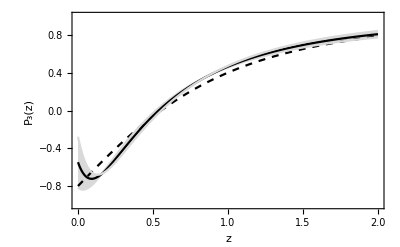

```mathematica
Plot[{P3wCDM[1/(1+z),-1,0.255,0.78],P3GA[1/(1+z)]+ϵ0 δP3GA[1/(1+z)]}//Evaluate,{z,0,2},Frame->True,PlotRange->{-1,1},PlotStyle->{{Dashed,Black},LightGray,Black,LightGray},Filling->{2->{{4},LightGray}},FrameStyle->Black,FrameLabel->{"z","P_3(z)"}]
```

```mathematica
Ωm0=1/(3NIntegrate[fs8GA[a]/fs8GA[1] NIntegrate[fs8GA[A]/(A fs8GA[1]),{A,0,a}],{a,0,1}])//Quiet
```

0.255531

```mathematica
ηGA[z_]:=(3P2GA[a] a^-3)/(2 EGA[a]^2(P3GA[a]+2+a D[Log[EGA[a]],a]))-1/.a->1/(1+z)
```

```mathematica
δηGA[z_]:=-((3 (EGA[a]^2 (-(2+P3GA[a]) δP2GA[a]+P2GA[a] δP3GA[a])+a P2GA[a] δEGA[a] EGA'[a]+EGA[a] (-a δP2GA[a] EGA'[a]+P2GA[a] (2 (2+P3GA[a]) δEGA[a]+a δEGA'[a]))))/(2 a^3 EGA[a]^2 (EGA[a] (2+P3GA[a])+a EGA'[a])^2))/.a->1/(1+z)//Abs
```

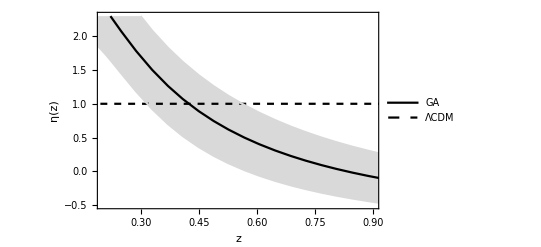

```mathematica
ploteta=Plot[{1,ηGA[z]+ϵ0 δηGA[z]}//Evaluate,{z,0.05,2},PlotStyle->{{Dashed,Black},LightGray,Black,LightGray},Frame->True,ImageSize->400,FrameLabel->{"z","η(z)"},FrameStyle->Black,BaseStyle->FontSize->16,PlotRange->{{0.2,0.9},{-0.5,2.3}},PlotLegends->Placed[LineLegend[{Black,{Dashed,Black}},{"GA","ΛCDM"}],Scaled[{0.8,0.8}]],Axes->None,Filling->{2->{{4},LightGray}}]
```

```mathematica
μGA[z_]:=(fGA[a]*P2GA[a])/((1+ηGA[z])Ωm0)/.a->1/(1+z)
δμGA[z_]:=1/(3 Ωm0)2 a^3 (EGA[a]^2 ((2+P3GA[a]) δfGA[a]+fGA[a] δP3GA[a])+a fGA[a] δEGA[a] EGA'[a]+EGA[a] (a δfGA[a] EGA'[a]+fGA[a] (2 (2+P3GA[a]) δEGA[a]+a δEGA'[a])))/.a->1/(1+z)//Abs
```

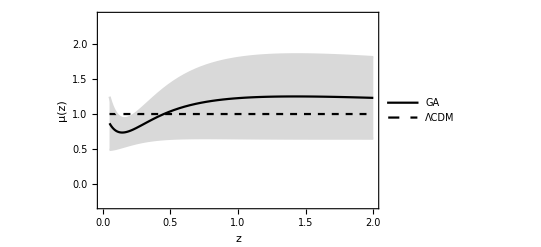

```mathematica
plotmu=Plot[{1,μGA[z]+ϵ0 δμGA[z]/.om->Ωm0}/.aa->1/(1+z)//Evaluate,{z,0.05,2},PlotStyle->{{Dashed,Black},LightGray,Black,LightGray},Frame->True,ImageSize->400,FrameLabel->{"z","μ(z)"},Filling->{2->{{4},LightGray}},FrameStyle->Black,BaseStyle->FontSize->16,PlotRange->{-0.3,2.4},PlotLegends->Placed[LineLegend[{Black,{Dashed,Black}},{"GA","ΛCDM"}],Scaled[{0.8,0.2}]],Axes->None]
```

```mathematica
Export["real_eta.pdf",ploteta,ImageSize->600]
Export["real_mu.pdf",plotmu,ImageSize->600]
```

real_eta.pdf

real_mu.pdf